## Prelab 4 Francesco Vassalli

### Q1

```mathematica
Grid[{{"Unit Gain f_T","5 MHz"},{"DC voltage gain","25 V/mV || 106 dB"},{"V_out Max","12-13V"},{"I_max","10 mA"},{"Input R","10^12Ω"}},Frame->All]
```

Unit Gain f_T | 5 MHz
DC voltage gain | 25 V/mV || 106 dB
V_out Max | 12-13V
I_max | 10 mA
Input R | 10^12Ω

### Q2

G_0=|V_out/V_in|=1+R_f/R

f_B=f_T/G_0

```mathematica
Subscript[G, 0][Rf_,R_]:=1+Rf/R;
Subscript[G, 0][10^4,10^2]
Subscript[G, 0][0,Infinity]
fT=5*10^6;
fB[Rf_,R_]:=fT/(Subscript[G, 0][Rf,R]);
N[fB[10^4,10^2]]
fB[0,Infinity]
```

101

1

49505.

5000000

```mathematica
Vout[Rf_,R_,Vin_]:=Vin*Subscript[G, 0][Rf,R];
"1 mV input"
N[Vout[10^4,10^2,10^-3]]
"1V input with 13V swing"
Therefore[Vout[10^4,10^2,1] ,13]
```

1 mV input

0.101

1V input with 13V swing

101∴13

In the DC limit the golden rule can be used to calculate the V_out.  However there is a 13V swing so the V_out will be limited to 13.

100.979

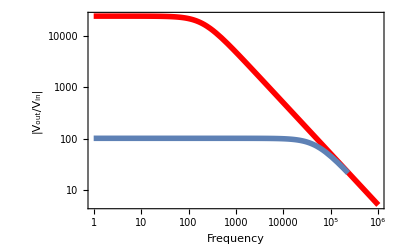

```mathematica
G[Rf_,R_,f_]:=Abs[(Subscript[G, 0][Rf,R])/(1+ⅉ*f/fB[Rf,R])];
Subscript[A, 0]=25*10^3;
f0=fT/Subscript[A, 0];
A[f_]:=Subscript[A, 0]/(1+ⅉ*f/f0);
N[Abs[G[10^4,100,1000]]]

Show[LogLogPlot[Abs[A[f]],{f,1,10^6},
Frame->True,Axes->True,
LabelStyle -> {FontFamily -> "Arial", FontSize -> 13},
FrameLabel -> {"Frequency", "|V_out/V_in|"},
FrameStyle -> Thickness[0.005],PlotStyle ->{Red, Thickness[0.01]},GridLines->All
],
LogLogPlot[Abs[G[10^4,100,f]],{f,1,10^6},PlotStyle->{Thickness[0.01]}]]
```

```mathematica
B[R_,Rf_]:=R/(R+Rf);
Ri0=10^12;
Ri[R_,Rf_,f_]:=Ri0*(1+A[f]*B[R,Rf]);
"Z_in:"
N[Ri[100,10^4,1000]]
```

Z_in:

1.05202×10^13-4.76009×10^13 ⅈ

```mathematica
Ro0=40;
Ro[R_,Rf_,f_]:=Ro0/(1+A[f]*B[R,Rf]);
"Z_out"
N[Ro[100,10^4,1000]]
```

Z_out

0.177069+0.801186 ⅈ

### Q3

I think that “debugging” the op-amp if we have it missed connected will be hard as I am not familiar with working with active elements.  Similarly the math will be different.  I am a little unsure about in what situations I shouldn’t be using the golden rule.  The derivation was a little fast for me.